```mathematica
sqrLen[v_]:=v.v
```

```mathematica
lerp[a_,b_,t_]:=a+(b-a)*t
```

```mathematica
bq[c1_,c2_,h_,t_]:=lerp[lerp[c1,h,t],lerp[h,c2,t],t]
```

```mathematica
bq2[c1_,c2_,t1_,t_]:=bq[c1,c2,c1+t1/2,t]
```

```mathematica
bq2D1[c1_,c2_,t1_,t_]=Simplify[D[bq2[c1,c2,t1,t],t]]
```

-2 c1 t+2 c2 t+t1-2 t t1

```mathematica
bq2D1[c1,c2,t1,1/2]
```

-c1+c2

```mathematica
bc[c1_,c2_,h1_,h2_,t_]:=lerp[lerp[lerp[c1,h1,t],lerp[h1,h2,t],t],lerp[lerp[h1,h2,t],lerp[h2,c2,t],t],t]
```

```mathematica
bc2[c1_,c2_,t1_,t2_,t_]:=bc[c1,c2,c1+t1/3,c2-t2/3,t]
```

```mathematica
bc2D1[c1_,c2_,t1_,t2_,t_]=Simplify[D[bc2[c1,c2,t1,t2,t],t]]
```

6 c1 (-1+t) t-6 c2 (-1+t) t+t1-4 t t1+3 t^2 t1-2 t t2+3 t^2 t2

```mathematica
Collect[bq[c1p,c2p,h,t],t]
```

c1p+(-2 c1p+2 h) t+(c1p+c2p-2 h) t^2

```mathematica
Collect[bc2D1[c1,c2,t1,t2,t],t]
```

t1+t (-6 c1+6 c2-4 t1-2 t2)+t^2 (6 c1-6 c2+3 t1+3 t2)

```mathematica
Solve[{c1p==t1,(-2 c1p+2 h)==(-6 c1+6 c2-4 t1-2 t2),(c1p+c2p-2 h) ==(6 c1-6 c2+3 t1+3 t2)},{c1p,c2p,h}]
```

{{c1p→t1,c2p→t2,h→-3 c1+3 c2-t1-t2}}

```mathematica
Solve[{{t1x,t1y,t1z}.{b1x,b1y,b1z}==0,{t2x,t2y,t2z}.{b2x,b2y,b2z}==0,bc2D1[{c1x,c1y,c1z},{c2x,c2y,c2z},{t1x,t1y,t1z},{t2x,t2y,t2z},t].bq[{b1x,b1y,b1z},{b2x,b2y,b2z},{sx,sy,sz},t]==0},{sx,sy,sz}]
```

{}

```mathematica
bc2D1[c1,c2,t1,t2,1/2*1]
```

-(3 c1)/2+(3 c2)/2-t1/4-t2/4

```mathematica
bc2Ap1[c1_,c2_,t1_,t2_,t_]:=bq2[c1,lerp[c1+t1/2,c2-t2/2,1/2],t1,t]
```

```mathematica
bc2Ap2[c1_,c2_,t1_,t2_,t_]:=bq2[c2,lerp[c1+t1/2,c2-t2/2,1/2],-t2,t]
```

```mathematica
bc2Ap1D1[c1_,c2_,t1_,t2_,t_]=D[bc2Ap1[c1,c2,t1,t2,t],t]
```

t1-(t t1)/2+t (-t1/2+1/2 (-c1+c2-t1/2-t2/2))+1/2 t (-c1+c2-t1/2-t2/2)

```mathematica
bc2Ap2D1[c1_,c2_,t1_,t2_,t_]=D[bc2Ap2[c1,c2,t1,t2,t],t]
```

t (c1-c2+t1/2+1/2 (-c1+c2-t1/2-t2/2)+t2/2)-t2+(t t2)/2+t (c1-c2+t1/2+1/2 (-c1+c2-t1/2-t2/2)+t2)

```mathematica
bc2Ap1D1[c1,c2,t1,t2,1]===-bc2Ap2D1[c1,c2,t1,t2,1]
```

True

```mathematica
bc2Ap1D2[c1_,c2_,t1_,t2_,t_]=Simplify[D[bc2Ap1[c1,c2,t1,t2,t],{t,2}]]
```

-c1+c2-(3 t1)/2-t2/2

```mathematica
bc2Ap2D2[c1_,c2_,t1_,t2_,t_]=Simplify[D[bc2Ap2[c1,c2,t1,t2,t],{t,2}]]
```

1/2 (2 c1-2 c2+t1+3 t2)

```mathematica
Solve[{bq2D1[c1,x1,t1,1]==th,bq2D1[x1,x2,th,1]==bq2D1[c2,x2,-t2,1]},{x1,x2}]
```

{}

```mathematica
Solve[{bq2D1[c1,x1,t1,1]==th1,bq2D1[x1,x2,th1,1]==th2,bq2D1[x2,x3,th2,1]==bq2D1[c2,x3,-t2,1]},{x1,x2,x3}]
```

{}

```mathematica
bq2D1[c1,x,t1,1]
```

-2 c1-t1+2 x

```mathematica
bq2D1[c2,x,-t2,1]
```

-2 c2+t2+2 x

```mathematica
a:={0,0}
```

```mathematica
b:={1,1}
```

```mathematica
at:={1,1}
```

```mathematica
bt:={1,-2}
```

```mathematica
Id[x_]:=x
```

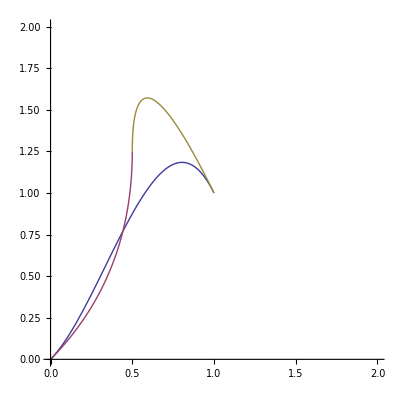

```mathematica
ParametricPlot[{bc2[a,b,at,bt,t],bc2Ap1[a,b,at,bt,t],bc2Ap2[a,b,at,bt,t]},{t,0,1},PlotRange->{{0,2},{0,2}}]
```

```mathematica
Solve[bc2D1[c1,c2,t1,t2,0][[2]]==t2*s,s]
```

Part::partd: Part specification t1 ⟦ 2 ⟧ is longer than depth of object.

{{s→t1⟦2⟧/t2}}

```mathematica
bi=Limit[Cross[bc2D1[{c1x,c1y,c1z},{c2x,c2y,c2z},{t1x,t1y,t1z},{t2x,t2y,t2z},t],bc2D1[{c1x,c1y,c1z},{c2x,c2y,c2z},{t1x,t1y,t1z},{t2x,t2y,t2z},t+o]]/o,o->0]
```

{2 (3 c1y t1z-3 c2y t1z-6 c1y t t1z+6 c2y t t1z+3 c1y t^2 t1z-3 c2y t^2 t1z+t1z t2y-3 t t1z t2y+3 t^2 t1z t2y-3 c1z ((-1+t)^2 t1y-t^2 t2y)+3 c2z ((-1+t)^2 t1y-t^2 t2y)-3 c1y t^2 t2z+3 c2y t^2 t2z-t1y t2z+3 t t1y t2z-3 t^2 t1y t2z),2 (-3 c1x t1z+3 c2x t1z+6 c1x t t1z-6 c2x t t1z-3 c1x t^2 t1z+3 c2x t^2 t1z-t1z t2x+3 t t1z t2x-3 t^2 t1z t2x+3 c1z ((-1+t)^2 t1x-t^2 t2x)-3 c2z ((-1+t)^2 t1x-t^2 t2x)+3 c1x t^2 t2z-3 c2x t^2 t2z+t1x t2z-3 t t1x t2z+3 t^2 t1x t2z),2 (3 c1x t1y-3 c2x t1y-6 c1x t t1y+6 c2x t t1y+3 c1x t^2 t1y-3 c2x t^2 t1y+t1y t2x-3 t t1y t2x+3 t^2 t1y t2x-3 c1y ((-1+t)^2 t1x-t^2 t2x)+3 c2y ((-1+t)^2 t1x-t^2 t2x)-3 c1x t^2 t2y+3 c2x t^2 t2y-t1x t2y+3 t t1x t2y-3 t^2 t1x t2y)}

```mathematica
Collect[bi[[1]],t]
```

2 t^2 (-3 c1z t1y+3 c2z t1y+3 c1y t1z-3 c2y t1z+3 c1z t2y-3 c2z t2y+3 t1z t2y-3 c1y t2z+3 c2y t2z-3 t1y t2z)+2 (-3 c1z t1y+3 c2z t1y+3 c1y t1z-3 c2y t1z+t1z t2y-t1y t2z)+2 t (6 c1z t1y-6 c2z t1y-6 c1y t1z+6 c2y t1z-3 t1z t2y+3 t1y t2z)

```mathematica
Collect[bi[[2]],t]
```

2 t (-6 c1z t1x+6 c2z t1x+6 c1x t1z-6 c2x t1z+3 t1z t2x-3 t1x t2z)+2 (3 c1z t1x-3 c2z t1x-3 c1x t1z+3 c2x t1z-t1z t2x+t1x t2z)+2 t^2 (3 c1z t1x-3 c2z t1x-3 c1x t1z+3 c2x t1z-3 c1z t2x+3 c2z t2x-3 t1z t2x+3 c1x t2z-3 c2x t2z+3 t1x t2z)

```mathematica
Collect[bi[[3]],t]
```

2 t^2 (-3 c1y t1x+3 c2y t1x+3 c1x t1y-3 c2x t1y+3 c1y t2x-3 c2y t2x+3 t1y t2x-3 c1x t2y+3 c2x t2y-3 t1x t2y)+2 (-3 c1y t1x+3 c2y t1x+3 c1x t1y-3 c2x t1y+t1y t2x-t1x t2y)+2 t (6 c1y t1x-6 c2y t1x-6 c1x t1y+6 c2x t1y-3 t1y t2x+3 t1x t2y)

```mathematica
bitan[c1x_,c1y_,c1z_,c2x_,c2y_,c2z_,t1x_,t1y_,t1z_,t2x_,t2y_,t2z_,t_]:={ t^2 (- c1z t1y+ c2z t1y+ c1y t1z- c2y t1z+ t1z t2y - t1y t2z + c1z t2y-c2z t2y- c1y t2z+ c2y t2z)+ t (2 c1z t1y-2 c2z t1y-2 c1y t1z+2 c2y t1z- t1z t2y+ t1y t2z)+ (- c1z t1y+ c2z t1y+ c1y t1z- c2y t1z+(1/3)*t1z t2y-(1/3)*t1y t2z), t^2 ( c1z t1x- c2z t1x- c1x t1z+ c2x t1z- t1z t2x+ t1x t2z - c1z t2x+ c2z t2x +c1x t2z- c2x t2z)+t (-2c1z t1x+2 c2z t1x+2 c1x t1z-2 c2x t1z+ t1z t2x- t1x t2z)+ ( c1z t1x- c2z t1x- c1x t1z+ c2x t1z-(1/3)*t1z t2x+(1/3)*t1x t2z), t^2 (- c1y t1x+ c2y t1x+ c1x t1y- c2x t1y+ t1y t2x- t1x t2y + c1y t2x- c2y t2x- c1x t2y+ c2x t2y)+ t (2 c1y t1x-2 c2y t1x-2 c1x t1y+2 c2x t1y- t1y t2x+ t1x t2y)+(- c1y t1x+ c2y t1x+ c1x t1y- c2x t1y+(1/3)*t1y t2x-(1/3)*t1x t2y) }
```

```mathematica
bitan[0,-1,0,0,1,0,1,0,0,-1,0,0,1/4]
```

{0,0,5/4}

```mathematica
Limit[Cross[bc2D1[{c1x,c1y,c1z},{c2x,c2y,c2z},{t1x,t1y,t1z},{t2x,t2y,t2z},t],bc2D1[{c1x,c1y,c1z},{c2x,c2y,c2z},{t1x,t1y,t1z},{t2x,t2y,t2z},t+o]]/sqrLen[Cross[bc2D1[{c1x,c1y,c1z},{c2x,c2y,c2z},{t1x,t1y,t1z},{t2x,t2y,t2z},t],bc2D1[{c1x,c1y,c1z},{c2x,c2y,c2z},{t1x,t1y,t1z},{t2x,t2y,t2z},t+o]]],o->0]
```

{DirectedInfinity[Sign[-6 c1z t1y+6 c2z t1y+12 c1z t t1y-12 c2z t t1y-6 c1z t^2 t1y+«19»+6 c2y t^2 t2z-2 t1y t2z+6 t t1y t2z-6 t^2 t1y t2z]/Sign[36 c1y^2 t1x^2+36 c1z^2 t1x^2-72 c1y c2y t1x^2+«802»+60 t^2 t1y^2 t2z^2-72 t^3 t1y^2 t2z^2+36 t^4 t1y^2 t2z^2]],DirectedInfinity[(«1»)/(«1»)],DirectedInfinity[Sign[-6 c1y t1x+«31»]/Sign[«1»]]}

```mathematica
Limit[Cross[bc2D1[{c1x,c1y,c1z},{c2x,c2y,c2z},{t1x,t1y,t1z},{t2x,t2y,t2z},t],bc2D1[{c1x,c1y,c1z},{c2x,c2y,c2z},{t1x,t1y,t1z},{t2x,t2y,t2z},t+o]]/sqrLen[bc2D1[{c1x,c1y,c1z},{c2x,c2y,c2z},{t1x,t1y,t1z},{t2x,t2y,t2z},t]-bc2D1[{c1x,c1y,c1z},{c2x,c2y,c2z},{t1x,t1y,t1z},{t2x,t2y,t2z},t+o]],o->0]
```

{ComplexInfinity,DirectedInfinity[Sign[3 c1z t1x-3 c2z t1x-6 c1z t t1x+6 c2z t t1x+3 c1z t^2 t1x-3 c2z t^2 t1x-3 c1x t1z+3 c2x t1z+6 c1x t t1z-6 c2x t t1z-3 c1x t^2 t1z+3 c2x t^2 t1z-3 c1z t^2 t2x+3 c2z t^2 t2x-t1z t2x+3 t t1z t2x-3 t^2 t1z t2x+3 c1x t^2 t2z-3 c2x t^2 t2z+t1x t2z-3 t t1x t2z+3 t^2 t1x t2z]/Sign[9 c1x^2+9 c1y^2+9 c1z^2-18 c1x c2x+9 c2x^2-18 c1y c2y+9 c2y^2-18 c1z c2z+9 c2z^2-36 c1x^2 t-36 c1y^2 t-36 c1z^2 t+72 c1x c2x t-36 c2x^2 t+72 c1y c2y t-36 c2y^2 t+72 c1z c2z t-36 c2z^2 t+36 c1x^2 t^2+36 c1y^2 t^2+36 c1z^2 t^2-72 c1x c2x t^2+36 c2x^2 t^2-72 c1y c2y t^2+36 c2y^2 t^2-72 c1z c2z t^2+36 c2z^2 t^2+12 c1x t1x-12 c2x t1x-42 c1x t t1x+42 c2x t t1x+36 c1x t^2 t1x-36 c2x t^2 t1x+4 t1x^2-12 t t1x^2+9 t^2 t1x^2+12 c1y t1y-12 c2y t1y-42 c1y t t1y+42 c2y t t1y+36 c1y t^2 t1y-36 c2y t^2 t1y+4 t1y^2-12 t t1y^2+9 t^2 t1y^2+12 c1z t1z-12 c2z t1z-42 c1z t t1z+42 c2z t t1z+36 c1z t^2 t1z-36 c2z t^2 t1z+4 t1z^2-12 t t1z^2+9 t^2 t1z^2+6 c1x t2x-6 c2x t2x-30 c1x t t2x+30 c2x t t2x+36 c1x t^2 t2x-36 c2x t^2 t2x+4 t1x t2x-18 t t1x t2x+18 t^2 t1x t2x+t2x^2-6 t t2x^2+9 t^2 t2x^2+6 c1y t2y-6 c2y t2y-30 c1y t t2y+30 c2y t t2y+36 c1y t^2 t2y-36 c2y t^2 t2y+4 t1y t2y-18 t t1y t2y+18 t^2 t1y t2y+t2y^2-6 t t2y^2+9 t^2 t2y^2+6 c1z t2z-6 c2z t2z-30 c1z t t2z+30 c2z t t2z+36 c1z t^2 t2z-36 c2z t^2 t2z+4 t1z t2z-18 t t1z t2z+18 t^2 t1z t2z+t2z^2-6 t t2z^2+9 t^2 t2z^2]],DirectedInfinity[Sign[-3 c1y t1x+3 c2y t1x+6 c1y t t1x-6 c2y t t1x-3 c1y t^2 t1x+3 c2y t^2 t1x+3 c1x t1y-3 c2x t1y-6 c1x t t1y+6 c2x t t1y+3 c1x t^2 t1y-3 c2x t^2 t1y+3 c1y t^2 t2x-3 c2y t^2 t2x+t1y t2x-3 t t1y t2x+3 t^2 t1y t2x-3 c1x t^2 t2y+3 c2x t^2 t2y-t1x t2y+3 t t1x t2y-3 t^2 t1x t2y]/Sign[9 c1x^2+9 c1y^2+9 c1z^2-18 c1x c2x+9 c2x^2-18 c1y c2y+9 c2y^2-18 c1z c2z+9 c2z^2-36 c1x^2 t-36 c1y^2 t-36 c1z^2 t+72 c1x c2x t-36 c2x^2 t+72 c1y c2y t-36 c2y^2 t+72 c1z c2z t-36 c2z^2 t+36 c1x^2 t^2+36 c1y^2 t^2+36 c1z^2 t^2-72 c1x c2x t^2+36 c2x^2 t^2-72 c1y c2y t^2+36 c2y^2 t^2-72 c1z c2z t^2+36 c2z^2 t^2+12 c1x t1x-12 c2x t1x-42 c1x t t1x+42 c2x t t1x+36 c1x t^2 t1x-36 c2x t^2 t1x+4 t1x^2-12 t t1x^2+9 t^2 t1x^2+12 c1y t1y-12 c2y t1y-42 c1y t t1y+42 c2y t t1y+36 c1y t^2 t1y-36 c2y t^2 t1y+4 t1y^2-12 t t1y^2+9 t^2 t1y^2+12 c1z t1z-12 c2z t1z-42 c1z t t1z+42 c2z t t1z+36 c1z t^2 t1z-36 c2z t^2 t1z+4 t1z^2-12 t t1z^2+9 t^2 t1z^2+6 c1x t2x-6 c2x t2x-30 c1x t t2x+30 c2x t t2x+36 c1x t^2 t2x-36 c2x t^2 t2x+4 t1x t2x-18 t t1x t2x+18 t^2 t1x t2x+t2x^2-6 t t2x^2+9 t^2 t2x^2+6 c1y t2y-6 c2y t2y-30 c1y t t2y+30 c2y t t2y+36 c1y t^2 t2y-36 c2y t^2 t2y+4 t1y t2y-18 t t1y t2y+18 t^2 t1y t2y+t2y^2-6 t t2y^2+9 t^2 t2y^2+6 c1z t2z-6 c2z t2z-30 c1z t t2z+30 c2z t t2z+36 c1z t^2 t2z-36 c2z t^2 t2z+4 t1z t2z-18 t t1z t2z+18 t^2 t1z t2z+t2z^2-6 t t2z^2+9 t^2 t2z^2]]}